```mathematica
data=Import["/home/phyks/hackEns/CitizenWatt/sample_emontxv2/1st_version/sample_power_only.log", "List"]
```

{478,477,477,477,477,476,476,478,476,478,476,477,478,477,476,477,476,477,475,476,452,452,451,452,450,450,449,449,449,449,450,450,450,447,450,451,449,450,450,448,448,449,448,449,451,449,447,448,448,448,447,458,448,448,472,445,447,445,447,446,444,446,445,444,446,447,447,445,444,444,444,445,445,445,«37927»,133,134,136,134,136,136,137,137,132,136,134,134,134,137,105,103,105,105,104,104,103,104,105,103,103,104,104,138,140,140,140,138,142,141,138,139,142,140,138,138,139,140,142,140,139,140,140,141,139,139,141,141,141,140,139,139,137,140,140,139,139,140,137,138,176,176,176,176,173,176,175,175,177,175}

```mathematica
Length[data]
```

38075

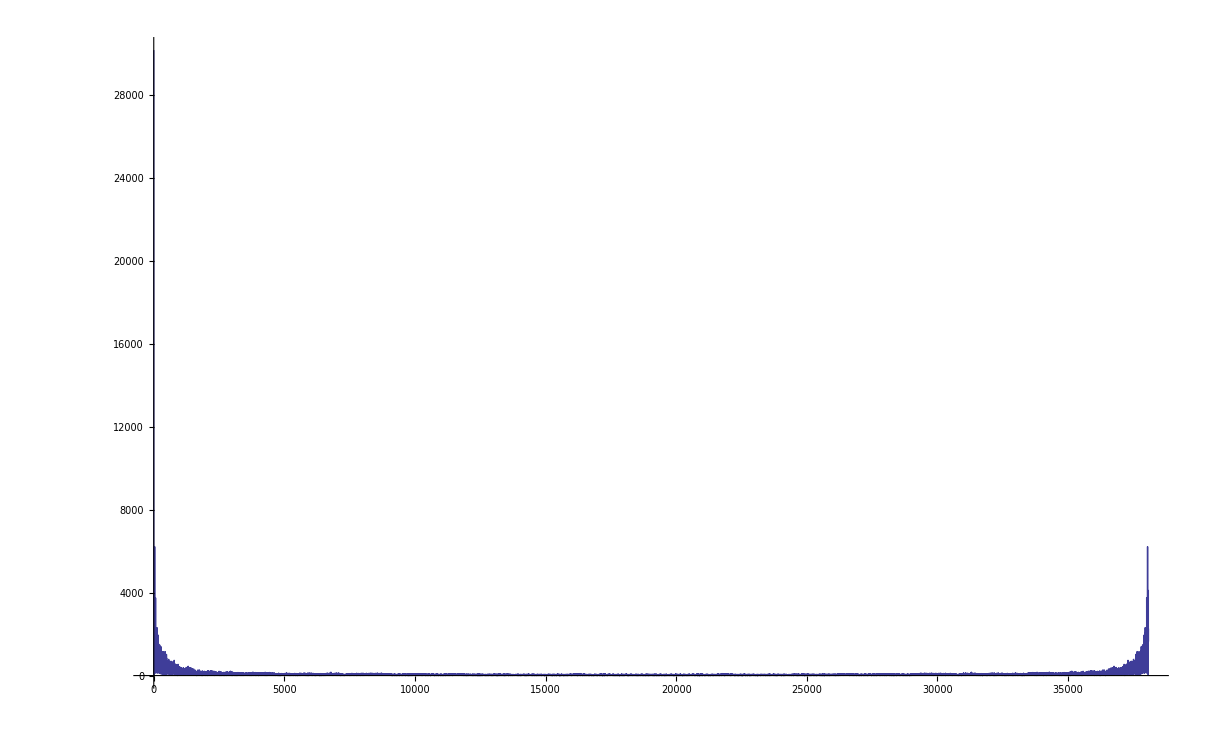

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->All]
```

```mathematica
ListLinePlot[data,PlotRange->All]
```

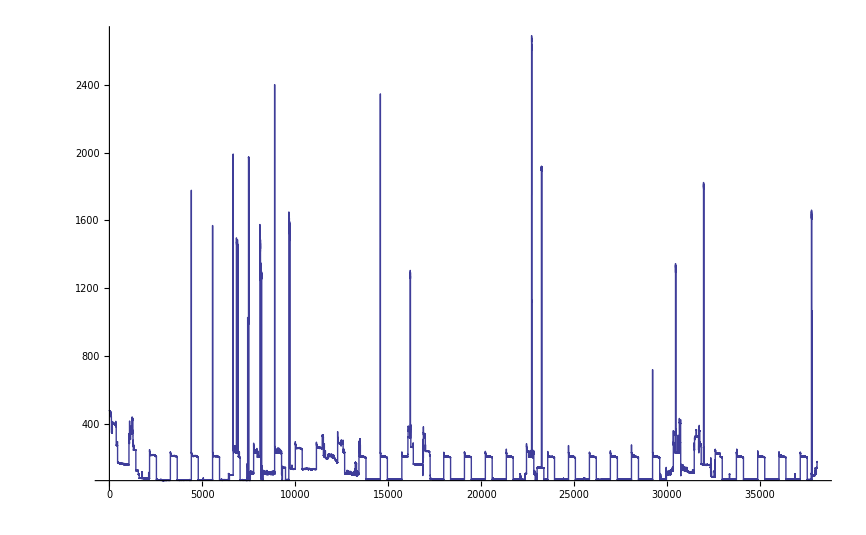
```mathematica
-Graphics-f
```

```mathematica
fftshift1D[array_]:=Module[{len=Length[array]},If[EvenQ[len],RotateRight[array,len/2],RotateRight[array,(len-1)/2]]]
```

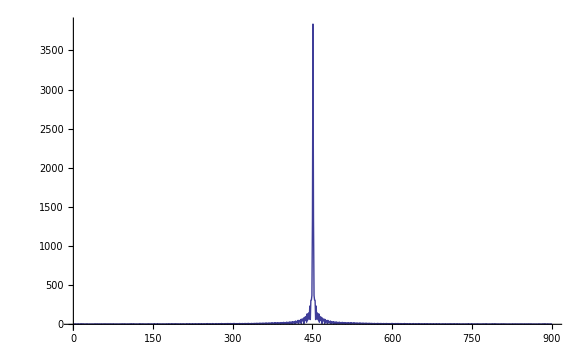

```mathematica
ListLinePlot[fftshift1D[Abs[Fourier[data[[2150;;3050]]]]], PlotRange->Full]
```

```mathematica
Max[Abs[Fourier[data[[1550;;3050]]]]]
```

4237.05

```mathematica
1/(2*%)
```

0.000118007